# 统计

## 直方图

## 数据集准备

```mathematica
irisData=ExampleData[{"MachineLearning","FisherIris"},"Data"];
{sepalLength,sepalWidth,petalLength,petalWidth}=Table[irisData[[i,1,j]],{j,1,4},{i,1,150}];(*不考虑标签*)
axeslabels=ExampleData[{"Statistics","FisherIris"},"ColumnHeadings"]
```

{SepalLength,SepalWidth,PetalLength,PetalWidth,Species}

## 直方图纵轴的选项

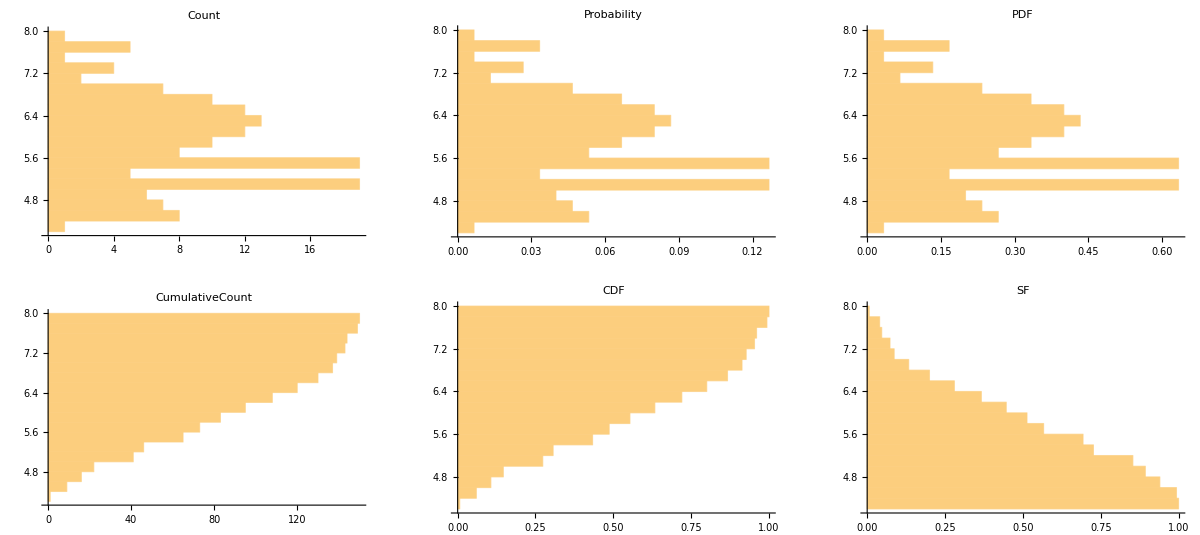

```mathematica
Table[Histogram[sepalLength,{.2},h,PlotLabel->h,BarOrigin->Left],{h,{"Count","Probability","PDF","CumulativeCount","CDF","SF"}}]//ArrayReshape[#,{2,3}]&//GraphicsGrid
```

## 概率密度估计曲线

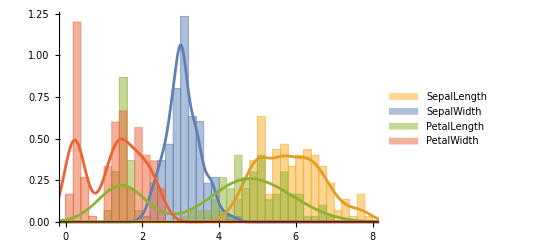

```mathematica
Show[Histogram[{sepalLength,sepalWidth,petalLength,petalWidth},{.2},"PDF",ChartLegends->Placed[axeslabels,Below]],SmoothHistogram[{sepalWidth,sepalLength(*Histogram和Plot的颜色顺序不同，这里调换了数据的顺序*),petalLength,petalWidth}]]
```

## 堆叠累积直方图

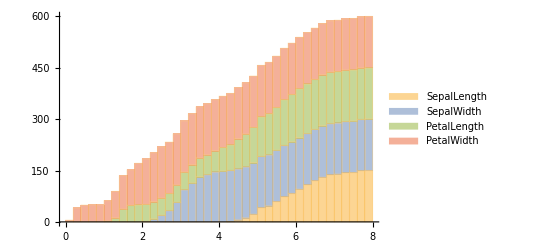

```mathematica
Histogram[{sepalLength,sepalWidth,petalLength,petalWidth},{.2},"CumulativeCount",ChartLegends->Placed[axeslabels,Below],ChartLayout->"Stacked"]
```

## 散点图

## 二维散点图

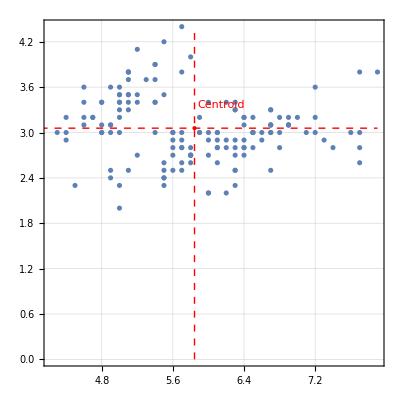

```mathematica
centroid=Mean[Transpose[{sepalLength,sepalWidth}]];
ListPlot[Transpose@{sepalLength,sepalWidth},AspectRatio->1,PlotTheme->"Detailed",Epilog->{(*绘制质心位置*)Red,PointSize[Large],Point[centroid],(*添加质心标注*)Text["Centroid",centroid+{0.3,0.3},{0,0}],(*绘制横向和纵向虚线*)Dashed,Line[{{centroid[[1]],0},{centroid[[1]],Max[sepalWidth]}}],(*纵向虚线*)Line[{{0,centroid[[2]]},{Max[sepalLength],centroid[[2]]}}]  (*横向虚线*)}]
```

## 二维数据直方图热图 二维 KDE 概率密度曲面等高线

```mathematica
{DensityHistogram[Transpose@{sepalLength,sepalWidth},{.2},"PDF"],SmoothDensityHistogram[Transpose@{sepalLength,sepalWidth},Mesh->20]}//GraphicsRow
```

-Graphics-

## 有标签数据可视化

## 平行坐标图

```mathematica
groupData=GroupBy[irisData,Last->First];
```

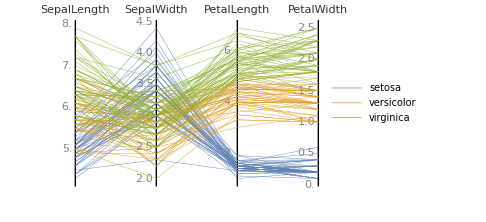

```mathematica
ParallelAxisPlot[groupData,PlotLegends->Automatic,ImageSize->Medium,AxesLabel->axeslabels]
```

```mathematica
newdata=Join[(*data*)#,
(*medium line*){Style[Median@#,Directive[Opacity[1],Thickness[0.01]]]},
(*quantile lines*)Style[#,Directive[Opacity[1],Dashed,Thickness[0.005]]]&/@Transpose@Quantile[#,{0.25,0.75}]]&/@groupData;
```

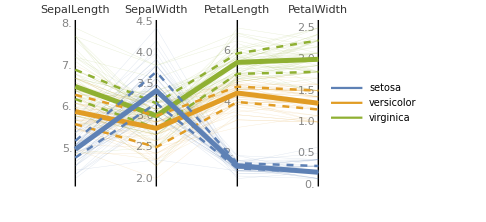

```mathematica
ParallelAxisPlot[newdata,PlotLegends->LineLegend[97,Keys[newdata]],PlotStyle->Opacity[0.2],AxesLabel->axeslabels,ImageSize->Medium]
```

## 箱型图

## 箱型图

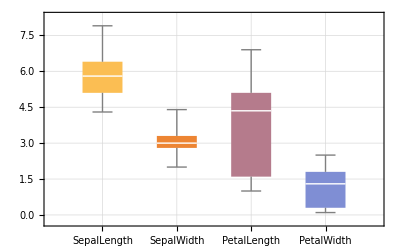

```mathematica
BoxWhiskerChart[{{sepalLength,sepalWidth,petalLength,petalWidth}}(*如果外面只有一层括号，则没有颜色区分*),ChartLabels->axeslabels,GridLines->Automatic]
```

## 小提琴图

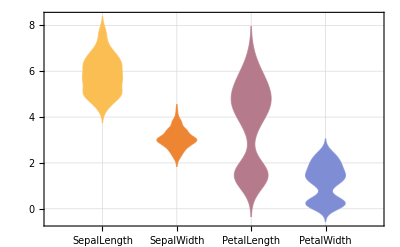

```mathematica
DistributionChart[{{sepalLength,sepalWidth,petalLength,petalWidth}},ChartLabels->axeslabels,GridLines->Automatic]
```

## 分布散点图

以下代码来自：https://mathematica.stackexchange.com/questions/133634/is-there-something-similar-to-seaborn-stripplot-in-mathematica

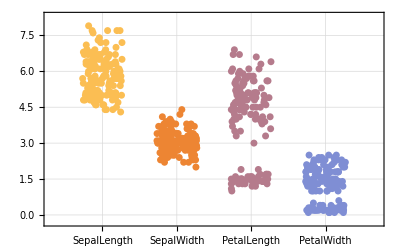

```mathematica
DistributionChart[{{sepalLength,sepalWidth,petalLength,petalWidth}},ChartLabels->axeslabels,ChartElementFunction->({AbsolutePointSize[5],Point[Transpose[{RandomReal[#1[[1]],Length[#2]],#2}]]}&),GridLines->Automatic]
```

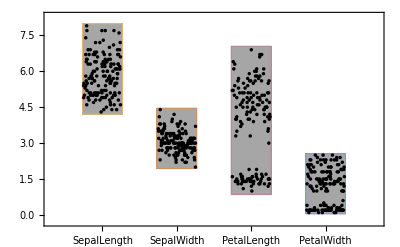

```mathematica
DistributionChart[{{sepalLength,sepalWidth,petalLength,petalWidth}},ChartLabels->axeslabels,ChartElementFunction->"PointDensity"]
```

## 多元随机变量关系

## 协方差矩阵

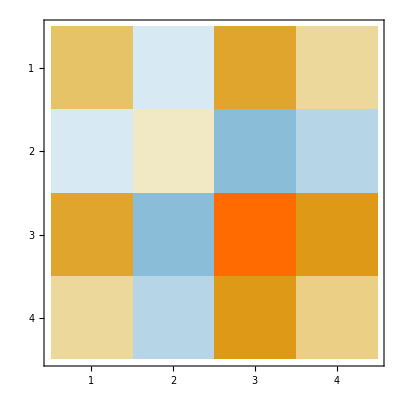
{-Graphics-,(0.685694 | -0.042434 | 1.27432 | 0.516271
-0.042434 | 0.189979 | -0.329656 | -0.121639
1.27432 | -0.329656 | 3.11628 | 1.29561
0.516271 | -0.121639 | 1.29561 | 0.581006)}

```mathematica
#@Covariance[irisData[[All,1,All]]]&/@{MatrixPlot,MatrixForm}
```

## 相关性系数矩阵

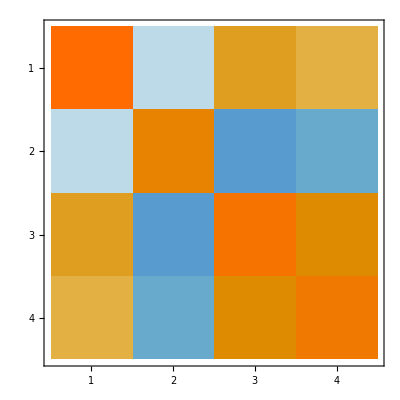
{-Graphics-,(1. | -0.11757 | 0.871754 | 0.817941
-0.11757 | 1. | -0.42844 | -0.366126
0.871754 | -0.42844 | 1. | 0.962865
0.817941 | -0.366126 | 0.962865 | 1.)}

```mathematica
#@Correlation[irisData[[All,1,All]]]&/@{MatrixPlot,MatrixForm}
```